```mathematica
res17 = NDSolve[{u'[x] == Sin[1.4*(u[x])^2]-x+v[x], v'[x] == x+u[x]-(2.2*(v[x])^2)+1, u[0] == 1, v[0] == 0.5}, {u,v}, {x, 0, 5}];
```

```mathematica
UV17 = Part[res17, 1];
U17 = Part[UV17, 1];
V17 = Part[UV17, 2];
```

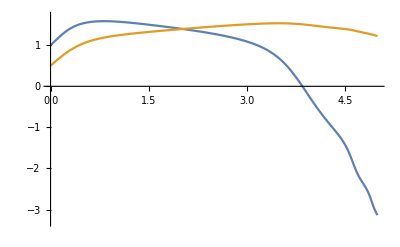

```mathematica
Plot[{u[x]/.U17, v[x]/.V17}, {x, 0, 5}, PlotRange->{-3.3, 1.7}]
```